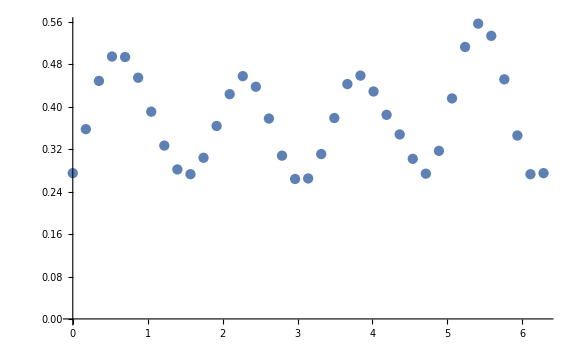

FittedModel[0.246411 (1+Cos[2 (0.868699+θ)]^2+0.0974547 Sin[2 (0.868699+θ)]^2)]

0.234465

0.00703715

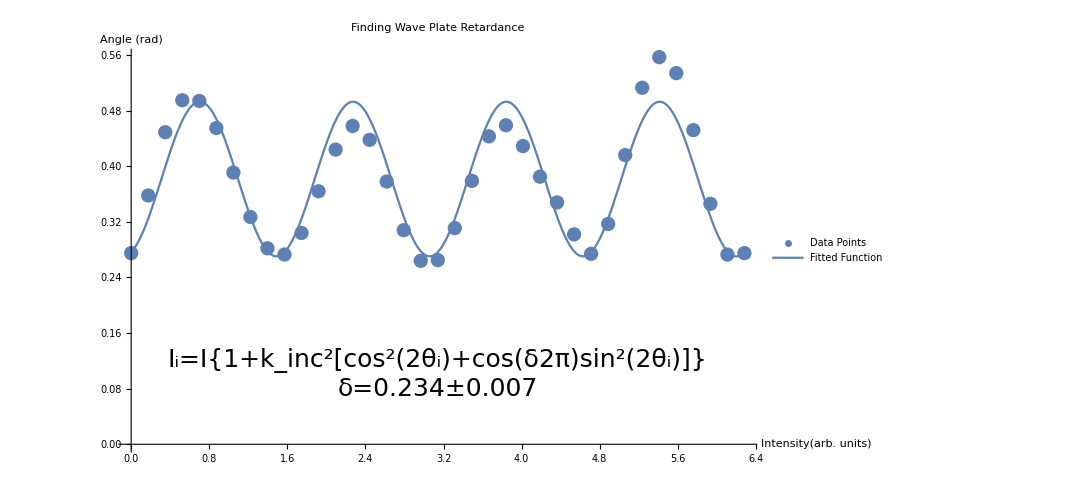

-Graphics-

```mathematica
(*First, we generate the angles at which the measurments were taken, in radians.*)
angles=Range[0,2π,10*π/180];
(*The intensity measurements collected*)
intensity={.275,.358,.449,.495,.494,.455,.391,.327,.282,.273,.304,.364,.424,.458,.438,.378,.308,.264,.265,.311,.379,.443,.459,.429,.385,.348,.302,.274,.317,.416,.513,.557,.534,.452,.346,.273,.275};
(*Matematica prefers data to be input in ordered pairs, this accomplishes that given our two lists*)
petersData=Transpose[{angles,intensity}];
(*Plot the data to make sure that things look as we expect them to.*)
ListPlot[petersData]

(*Clear the variables that are used as fit parameters, just in case a value is already stored in there
which would prevent it from being fit.*)
Clear[i,δ, int]
(*Previous data collected indicated our extinction ratio is equal to 1*)
kinc=1;
(*The functional model that we expect the data to match *)
deltaQWPModel=int(1+kinc^2(Cos[2(θ+θo)]^2+Cos[δ ] Sin[2(θ+θo)]^2));

(*Fit the data to the functional model. δ, θo, and int are the fitting parameters.
Our independent variable is θ. *)
fit =NonlinearModelFit[petersData,deltaQWPModel,{δ,θo,int},θ]

(*We want to know our answer as a fraction of a full wave, which is 2π*)
fullWave=2π;

(*Print out the retardance, as a fraction of a full wave.*)
δ/fullWave/.fit["BestFitParameters"]
(*Print out the error, as a fraction of a full wave *)
error=fit["ParameterErrors"][[1]]/fullWave

(*Create a text string to show information about the fit on our graph*)
fitInfo=StringForm["I_i=I{1+k_inc^2[cos^2(2θ_i)+cos(δ2π)sin^2(2θ_i)]}\nδ=``±``",NumberForm[δ/fullWave/.fit["BestFitParameters"],3],NumberForm[error,1]];
(*Store where we want to place the text string *)
textPos={π,.1};
(*Show both the data and the fit to the data *)
plot=Show[{ListPlot[Legended[petersData,"Data Points"],PlotLabel->Style["Finding Wave Plate Retardance",24],AxesLabel->{"Intensity(arb. units)","Angle (rad)"},LabelStyle->24,ImageSize->{800,Automatic}],Plot[Legended[deltaQWPModel/.fit["BestFitParameters"],"Fitted Function"],{θ,0,2π},LabelStyle->24],Graphics[Text[Style[fitInfo,25],textPos]]}]
(*In order to export the graph with the legend, we have to rasterize the image so that it is all combined into one.*)
Rasterize[plot]
```